```mathematica
Lor[ϵ_,Γ_,ϵ0_]:= Γ/( (ϵ-ϵ0)^2 +(Γ^2/4) )
FermiDirac[ϵ_,β_,μ_]:= 1/(Exp[β*(ϵ-μ)]+1)
```

```mathematica
Γr = 0.2;
Γl = 0.2;
μR = -0.5;
μL = 0.5;
ω = 0.05;
```

```mathematica
ϵd0 = -0.2;
ϵa0 = 0.4;
```

```mathematica
iLR01[ϵ_,β_]:=FermiDirac[ϵ,μL,β]*Lor[ϵ,Γl,ϵd0+μL]*(1-FermiDirac[ϵ-ω,μR,β])*Lor[ϵ-ω,Γr,ϵa0+μR]
```

```mathematica
iLR10[ϵ_,β_]:=FermiDirac[ϵ,μL,β]*Lor[ϵ,Γl,ϵd0+μL]*(1-FermiDirac[ϵ+ω,μR,β])*Lor[ϵ+ω,Γr,ϵa0+μR]
```

```mathematica
iRL01[ϵ_,β_]:=FermiDirac[ϵ,μR,β]*Lor[ϵ,Γr,ϵa0+μR]*(1-FermiDirac[ϵ-ω,μL,β])*Lor[ϵ-ω,Γl,ϵd0+μL]
```

```mathematica
iRL10[ϵ_,β_]:=FermiDirac[ϵ,μR,β]*Lor[ϵ,Γr,ϵa0+μR]*(1-FermiDirac[ϵ+ω,μL,β])*Lor[ϵ+ω,Γl,ϵd0+μL]
```

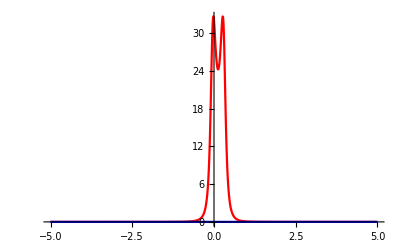

```mathematica
Plot[{iLR01[ϵ,25],iRL01[ϵ,25]},{ϵ,-5,5},PlotRange->All,PlotStyle->{Red, Blue}]
```

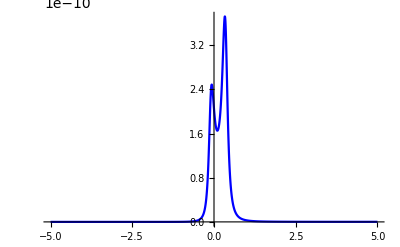

```mathematica
Plot[{iRL01[ϵ,25]},{ϵ,-5,5},PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
iRL01[0.1,25]
```

(5.98779×10^-11 ΓL)/(0.0625+ΓL^2/4)